11

{1+(-1+ξ/2) (1+ξ),(1-ξ) (1+ξ),1/2 ξ (1+ξ)}

{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}

{{11.6933,-13.32,1.66},{-13.32,26.7733,-13.32},{1.66,-13.32,11.6933}}

{Null,Null,Null}

{0.0333333,0.133333,0.0333333}

{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}

{0,0,0,0,0,0,0,0,0,0,0}

0

0

0.133333

0.0666667

0.133333

0.0666667

{1,0,0}

{1,0,0}

{0,0,1}

{0,0,1}

{0.,0.0412853,0.0729739,0.0953861,0.108743,0.113182,0.108743,0.0953861,0.0729739,0.0412853,0.}

{}

{0.}

{0.,0.0412853,0.0729739,0.0729739,0.0953861,0.108743,0.108743,0.113182,0.108743,0.108743,0.0953861,0.0729739,0.0729739,0.0412853,0.}

{y[x]→-(ⅇ^-x (-1+ⅇ^x) (-ⅇ+ⅇ^x))/(1+ⅇ)}

-(ⅇ^-x (-1+ⅇ^x) (-ⅇ+ⅇ^x))/(1+ⅇ)

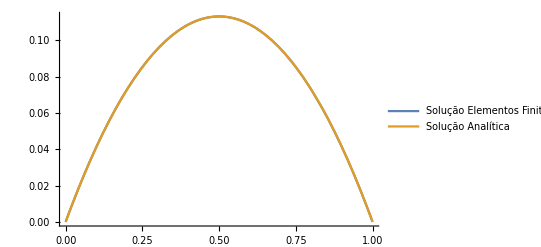

0.0278605

0.254372

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
GaussQ[g_,n_,a_,b_]:=Total[g[First[#]]*Last[#]&/@GaussianQuadratureWeights[n,a,b]]
α=1;γ=1;
u0=0;u1=0;
n=5;h=1/n;np=4;m=n*2+1
φ={InterpolatingPolynomial[{{-1,1},{0,0},{1,0}},ξ],InterpolatingPolynomial[{{-1,0},{0,1},{1,0}},ξ],InterpolatingPolynomial[{{-1,0},{0,0},{1,1}},ξ]}
K={{,,},{,,},{,,}}
K=α*(2/h)*Table[GaussQ[D[φ[[r]],ξ]*D[φ[[s]],ξ]/.ξ->#&,np,-1,1],{r,3},{s,3}]+γ*(h/2)*Table[GaussQ[φ[[r]]*φ[[s]]/.ξ->#&,np,-1,1],{r,3},{s,3}]
F={,,}

F=(h/2)*Table[GaussQ[φ[[r]]/.ξ->#&,np,-1,1],{r,3}]
K1=ConstantArray[0,{m,m}]
For[i=1,i<m-1,i=i+2,
K1[[i;;i+2,i;;i+2]]=K1[[i;;i+2,i;;i+2]]+K;

]
F1=ConstantArray[0,{m}]
For[i=1,i<m,i=i+2,
F1[[i;;i+2]]=F1[[i;;i+2]]+F

]
F1[[1]]=u0
F1[[m]]=u1
F1[[2]]=F1[[2]]-K1[[2,1]]*u0
F1[[3]]=F1[[3]]-K1[[3,1]]*u0
F1[[m-1]]=F1[[m-1]]-K1[[m-1,m]]*u1
F1[[m-2]]=F1[[m-2]]-K1[[m-2,m]]*u1
K1[[1,1;;3]]={1,0,0}
K1[[1;;3,1]]={1,0,0}
K1[[m,m-2;;m]]={0,0,1}
K1[[m-2;;m,m]]={0,0,1}

w=LinearSolve[K1,F1]

LagrangeP[p1_]:={Piecewise[{{InterpolatingPolynomial[{{p1,1},{p1+h/2,0},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h/2,1},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h/2,0},{p1+h,1}},x],p1<=x≤p1+h}},0]}

ϕ={}
For[i=1,i<=n,i++,
AppendTo[ϕ,LagrangeP[(i-1)*h][[1]]];
AppendTo[ϕ,LagrangeP[(i-1)*h][[2]]];
AppendTo[ϕ,LagrangeP[(i-1)*h][[3]]]
]

W1={w[[1]]}
For[i=2,i<m,i++,
W1=Join[W1,ConstantArray[w[[i]],{Mod[i,2]+1}]]
]
W1=Join[W1,{w[[m]]}]
Clear[Uh]
Uh[x_]:=W1.ϕ
solution=DSolve[{-α*y''[x]+γ*y[x]==1,y[0]==u0,y[1]==u1},y[x],x][[1]]
u[x_]=y[x]/.solution[[1]]
Plot[{Uh[x],u[x]},{x,0,1},PlotRange->All,ImageSize->400,PlotLegends->{"Solução Elementos Finitos","Solução Analítica"},AxesStyle->Black]
G[x_]:=(u[x]-Uh[x])^2
(Sum[h/2*Sum[GaussianQuadratureWeights[4,-1,1][[l]][[2]]*(G[x]/.x->(i*h+h/2*(GaussianQuadratureWeights[4,-1,1][[l]][[1]]+1))),{l,1,4}],{i,0,n}])^(1/2)
G1[x_]:=(D[u[x],x]-D[Uh[x],x])^2
(Sum[h/2*Sum[GaussianQuadratureWeights[4,-1,1][[l]][[2]]*(G1[x]/.x->(i*h+h/2*(GaussianQuadratureWeights[4,-1,1][[l]][[1]]+1))),{l,1,4}],{i,0,n}])^(1/2)
```

```mathematica
G[x_]:=(u[x]-Uh[x])^2
```

```mathematica
(Sum[h/2*Sum[GaussianQuadratureWeights[4,-1,1][[l]][[2]]*(G[x]/.x->(i*h+h/2*(GaussianQuadratureWeights[4,-1,1][[l]][[1]]+1))),{l,1,4}],{i,0,n}])^(1/2)
```

0.0204359

```mathematica
G1[x_]:=(D[u[x],x]-D[Uh[x],x])^2
```

```mathematica
(Sum[h/2*Sum[GaussianQuadratureWeights[4,-1,1][[l]][[2]]*(G1[x]/.x->(i*h+h/2*(GaussianQuadratureWeights[4,-1,1][[l]][[1]]+1))),{l,1,4}],{i,0,n}])^(1/2)
```

0.193586